```mathematica
(*sc=Il/Isat;
T=Ia/Il;
*)
Clear[T,sc]
soln=FullSimplify[Solve[b==-(α0+b α1 + b^2 α2)Log[T]+sc(1-T),b]][[2]][[1]]
```

b→1/(2 α2 Log[T])(-1-α1 Log[T]+√(-4 α2 Log[T] (sc (-1+T)+α0 Log[T])+(1+α1 Log[T])^2))

```mathematica
soln1=Simplify[Solve[b==-(α0+b α1 )Log[T]+sc(1-T),b]][[1]][[1]]
```

b→(sc-sc T-α0 Log[T])/(1+α1 Log[T])

```mathematica
sc=Il/Isat;
T=Ia/Il;
solnrl=FullSimplify[Solve[b==-(α0+b α1 + b^2 α2)Log[T]+sc(1-T),b]][[2]][[1]][[2]]
```

(-1-α1 Log[Ia/Il]+√(-(4 α2 Log[Ia/Il] (Ia-Il+Isat α0 Log[Ia/Il]))/Isat+(1+α1 Log[Ia/Il])^2))/(2 α2 Log[Ia/Il])

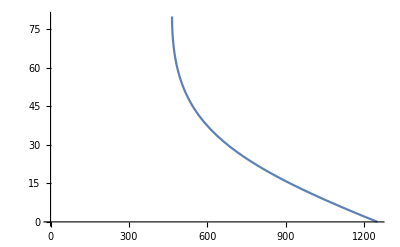

```mathematica
Plot[solnrl/.{Isat->25,α0->1.23,α1->0.19,α2->0.0051,Il->50*25},{Ia,0,50*25}]
```

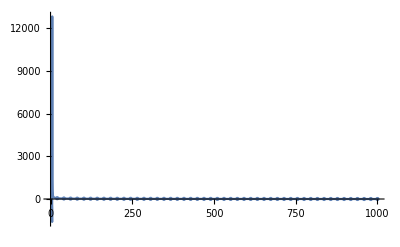

```mathematica
solnrl1=Simplify[Solve[b==-(α0+b α1 )Log[T]+sc(1-T),b]][[1]][[1]][[2]];Plot[solnrl1/.{Isat->100,α0->1.23,α1->0.19,α2->0.0051,Il->1000},{Ia,0,1000},Mesh->Full,PlotRange->All]
```

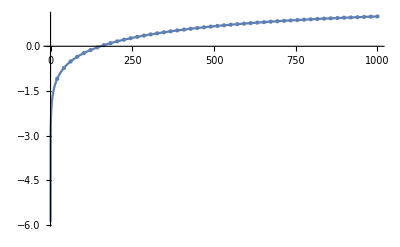

```mathematica
arg=-(4 α2 Log[Ia/Il] (Ia-Il+Isat α0 Log[Ia/Il]))/Isat+(1+α1 Log[Ia/Il])^2;
Plot[arg/.{Isat->100,α0->1.23,α1->0.19,α2->0.0051,Il->1000},{Ia,0,1000},Mesh->Full,PlotRange->All]
```

```mathematica
Solve[arg==0,Ia,Reals,Assumptions->{Il>0,α0>0,α1>0,α2>0,Isat>0}]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[-(4 α2 Log[Ia/Il] (Ia-Il+Isat α0 Log[Ia/Il]))/Isat+(1+α1 Log[Ia/Il])^2==0,Ia,ℝ,Assumptions→{Il>0,α0>0,α1>0,α2>0,Isat>0}]